# Ukázka využití Schlömilchovy věty na přerovnání řady

Simona Buryšková, Jan Hrubeš

## Section Zkoumaná řada

Vypíšeme si pro představu několik prvních členů zkoumané řady:

```mathematica
clenyUkazka = Table[(-1)^(k-1)/k, {k,1,10}]
cleny = Table[(-1)^(k-1)/k, {k,1,100}];
```

{1,-1/2,1/3,-1/4,1/5,-1/6,1/7,-1/8,1/9,-1/10}

Posloupnost částečných součtů pro prvních 100 členů vypadá takto (zkráceně):

```mathematica
castecnesoucty = Accumulate[cleny];
Short[castecnesoucty,3]
```

{1,1/2,5/6,7/12,«93»,9594516020402274303348963549166209678997/13944075045942495432906761787062460711360,9735365263290582338024789425803204231637/13944075045942495432906761787062460711360,47979622564155786918478609039662898122617/69720375229712477164533808935312303556800}

Řada je neabsolutně konvergentní1 (harmonická řada totiž diverguje) a platí .

Konvergenci posloupnosti částečných součtů k součtu řady znázorňuje Graf 1.

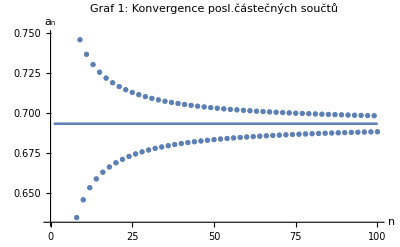

```mathematica
castecnesouctyPlot = ListPlot[castecnesoucty];
limitaPuvodni= Plot[Log[2], {x, 1, 100}];
Show[castecnesouctyPlot, limitaPuvodni,%21,AxesLabel->{HoldForm[],HoldForm[]},PlotLabel->HoldForm["Graf 1: Konvergence posl.částečných součtů"],LabelStyle->{GrayLevel[0]}]
```

## Section Přerovnání řady pomocí Schlömilchova algoritmu

Abychom ukázali, že naši neabsolutně konvergentní lze přerovnat tak, že součet přerovnané řady bude jiný než součet nepřerovnané, využijeme Schlömilchovu větu2 , která je speciální variantou Riemannovy věty a zabývá se přerovnáním alternující řady.

Věta (Schlömilch(1873)): Nechť  je klesající funkce taková, že  a nechť  je definováno jako:  Nechť alternující řada  je konvergentní a její součet budeme značit  . Přerovnejme tuto řadu podle následujícího postupu:
- Vezměme prvních  kladných členů řady a JAK TO MÁM INTELIGENTNĚ ŘÍCT???      Na prvních p míst přerovnané řady dejme prvních p kladných členů řady původní, na dalších q míst dejme prvních q záporných členů původní řady a takto pokračujme dál. Vždy vezměme dalších p kladných členů a přidejme je do přerovnané řady a stejně tak dalších q záporných členů.
- Vezměme prvních  kladných členů řady a ???
- Opakujme první dva kroky s takto modifikovanou řadou.
Pak tímto postupem přerovnaná řada konverguje a jejím součtem je .

V našem případě je zjevně  a zvolíme za parametry  a  (poznámka: JAK MÁM VOLIT p,q A CO KDYŽ p=q???)(p,q se volí libovolně a když p=q tak vyjde člen navíc nulový a součet zůstane stejný. Dle Věty získáme tímto přerovnáním řadu se součtem .
Přerovnání provedeme následující sekvencí příkazů:

```mathematica
K = 1;
p = 3; q = 2; (* volba parametrů*)
kladne = Select[cleny, #>0&]; (*výběr kladných/záporných členů*)
zaporne = Select[cleny, #<0&];
kladneSkupiny = Partition[kladne,p]; (*seskupení kladných/záporných členů do p- resp. q-členných skupin*)
zaporneSkupiny =Partition[zaporne,q];
prerovnani= Table[{kladneSkupiny[[i]], zaporneSkupiny[[i]]}, {i, 1,16}]; (* PROČ 16??? protože 100/2=50,50/3=16,xx*)
prerovnani = Flatten[prerovnani]; (*odstranění závorek*)
castecneSouctyPrerovnane = Accumulate[prerovnani]; (*posloupnost částečných součtů přerovnané řady*)
```

Nyní si vypišme, jak vypadá řada po přerovnání:

```mathematica
Short[prerovnani,3]
```

{1,1/3,1/5,-1/2,-1/4,1/7,1/9,1/11,-1/6,-1/8,1/13,1/15,1/17,-1/10,-1/12,1/19,«49»,1/79,1/81,1/83,-1/54,-1/56,1/85,1/87,1/89,-1/58,-1/60,1/91,1/93,1/95,-1/62,-1/64}

Konvergenci posloupnosti částečných součtů k číslu  znázorňuje Graf 2:

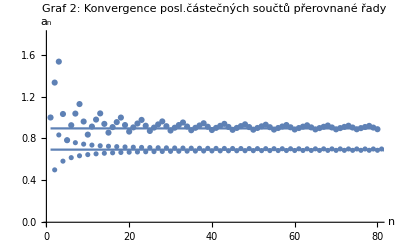

```mathematica
(*PROČ TO VYKRESLÍ I DATA NEPŘEROVNANÉ???*)
castecneSouctyPrerovnanePlot = ListPlot[castecneSouctyPrerovnane];
limita= Plot[Log[2] + 1/2*Log[p/q], {X, 1, Length[castecneSouctyPrerovnane]}];
Show[limita, castecneSouctyPrerovnanePlot,%21,AxesLabel->{HoldForm[],HoldForm[]},PlotLabel->HoldForm["Graf 2: Konvergence posl.částečných součtů přerovnané řady"],LabelStyle->{GrayLevel[0]}]
```

## Section Závěr

Byla zkoumána neabsolutně konvergentní řada . Jejím přerovnáním dle Schlömilchovy věty jsme získali řadu o součtu , což demonstruje fakt, že po přerovnání členů nemusí mít řada stejný součet jako před přerovnáním. Výsledky byly graficky znázorněny v Grafu 1 a 2.

## Section Zdroje

1	KOPÁČEK, Jiří. Matematická analýza nejen pro fyziky (II). 4. vyd. Praha: Matfyzpress, 2015. ISBN 978-80-7378-282-5.

2	PRŮŠA V., TŮMA K. Rearrangement of non-absolute convergent series - how to prove that 1 = 2. MFF UK, 2022.